```mathematica
input:="%fk %xh 
%mq %pr 
%pb %kq 
%zt %pb &bt 
%qz &ml %kh 
&ml %kp %sr %tq &nb %tk %sh %vk 
%hq %bb 
%cq &gp %mq 
&ls &lg 
%tk %sh 
%ph &rb %hx 
%rt %hq 
&lg &rx 
%lx %ff &gp 
%nt %gs &gp 
%tp &gp %lx 
%nv %xm 
%kh &ml 
%bn %sv &bt 
%sj %kj &rb 
%ps %qz &ml 
&gp %df &ls %mq %tp %nv 
%hx &rb 
%vk %tk 
%qr &bt %zt 
%dx &bt %tz 
%kj %fk 
broadcaster %sj %sr %tp %nk 
%xf %qr 
%zk &ml %ps 
%xh %zs &rb 
%zs %ct 
%jm &ml %kp 
%pr &gp %pf 
%tq %jm 
%ff &gp %df 
%df %nv 
%vs %tq &ml 
&vg &lg 
&rx 
%xm &gp %cq 
&vc &lg 
%tl %bn 
%sr %vs &ml 
%nk %nn &bt 
%tz &bt 
%nn %xf &bt 
%kp %vk 
&bt %tl %nk %pb %xf &vg 
%kf &rb %ph 
&nb &lg 
%bb %kf &rb 
%sh %zk 
%kq %tl &bt 
%sv %dx &bt 
%gs &gp 
&rb &vc %zs %fk %hq %rt %sj %kj 
%pf &gp %nt 
%ct %rt &rb"
```

```mathematica
isNotEmpty[s_]:=s!=""
```

```mathematica
lines:=StringSplit[input,"\n"]
adj:=Select[isNotEmpty][StringSplit[#," "]]&/@lines
edges:=Flatten[Table[DirectedEdge[#[[1]],#[[i]]],{i,2,Length[#]}]&/@adj]
```

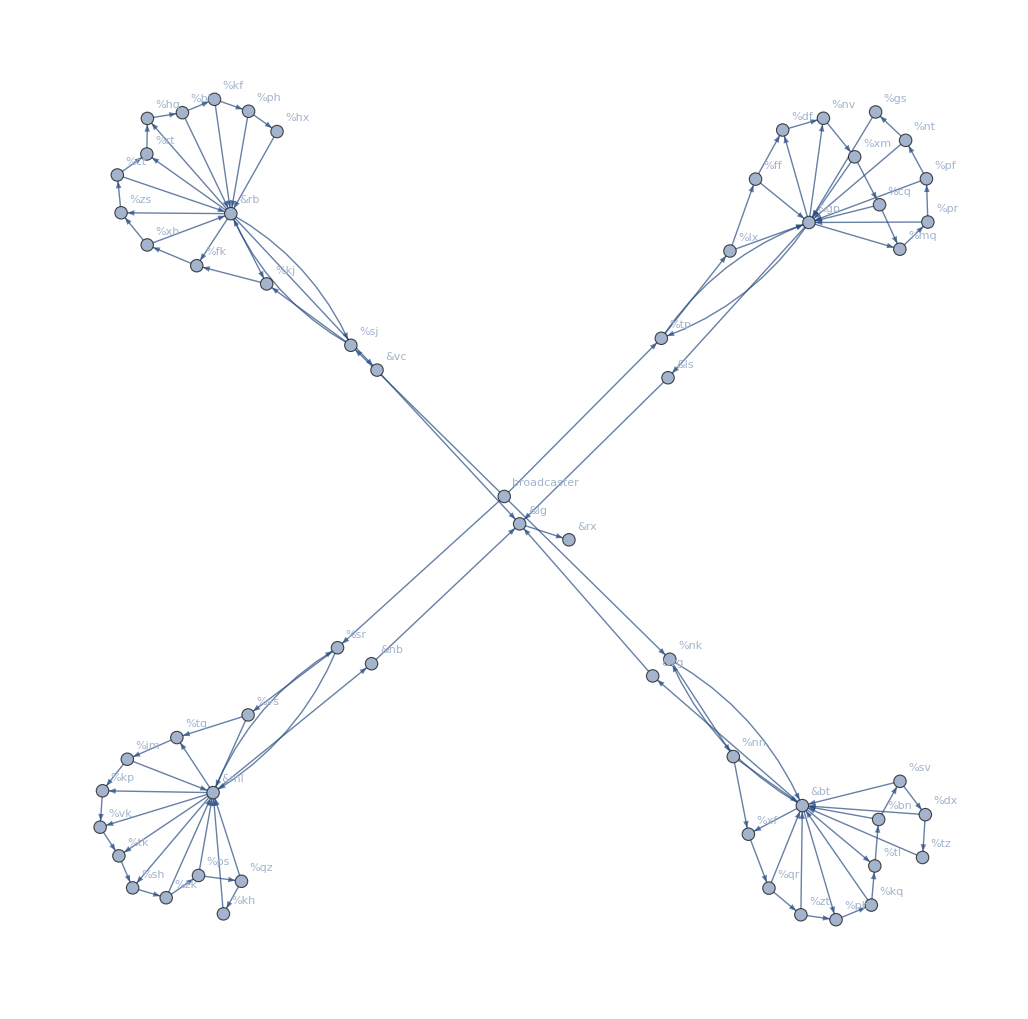

```mathematica
Graph[edges,VertexLabels->"Name"]
```

```mathematica
G=Graph[edges,VertexLabels->"Name",VertexShapeFunction->{"broadcast"->"Triangle",_?(StringContainsQ["%"])->"Star",_?EvenQ->"Square"},VertexSize->Medium];
```